```mathematica
a=4.35196*10^6;
b=0.030554;
e=1;
H0=a/e*{{0,0,0},{0,b,0},{0,0,1}};
H0//MatrixForm
```

(0. | 0. | 0.
0. | 132970. | 0.
0. | 0. | 4.35196×10^6)

```mathematica
γ=6.5956*10^4;
n=10.54;
u[ξ_]:=γ*ⅇ^(-1*n *ξ)
s12=Sqrt[0.308];
s23=Sqrt[0.437];
s13=Sqrt[0.0234];
c12=Sqrt[1-s12^2];
c23=Sqrt[1-s23^2];
c13=Sqrt[1-s13^2];
W={{c13^2*c12^2,c12*s12*c13^2,c12*c13*s13},{c12*s12*c13^2,s12^2*c13^2,s12*c13*s13},{c12*s13*c13,s12*c13*s13,s13^2}};
W//MatrixForm
```

(0.675807 | 0.450864 | 0.125753
0.450864 | 0.300793 | 0.0838961
0.125753 | 0.0838961 | 0.0234)

```mathematica
DOPRICoeffs[5,p_]:=N[{{{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}},{35/384,0,500/1113,125/192,-2187/6784,11/84,0},{1/5,3/10,4/5,8/9,1,1},{71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40}},p];
```

```mathematica
ψ[ξ_]:={ψ1[ξ],ψ2[ξ],ψ3[ξ]}
```

```mathematica
sol=NDSolve[{ⅈ*D[ψ[ξ],ξ]==(H0+u[ξ]*W).ψ[ξ],ψ[0.1]=={c12 c13,s12 c13, s13}},{ψ1,ψ2,ψ3},{ξ,0.1,1}, Method->{"ExplicitRungeKutta","Coefficients"->DOPRICoeffs,"DifferenceOrder"->5,"StiffnessTest"->False},StartingStepSize->0.25,MaxSteps->Infinity,MaxStepFraction->1/12,WorkingPrecision->MachinePrecision,AccuracyGoal->Infinity];
```

```mathematica
uf[x_]:= Evaluate[{ψ1[ξ],ψ2[ξ],ψ3[ξ]}/.sol]/.{ξ->x}/.{ξ_}->ξ;
```

```mathematica
quf[v_]:=Abs[v[[1]]]^2+Abs[v[[2]]]^2+Abs[v[[3]]]^2;
```

```mathematica
absuf[v_] := {Abs[v[[1]]]^2,Abs[v[[2]]]^2,Abs[v[[3]]]^2};
```

```mathematica
reimuf[v_]:={Re[v[[1]]],Im[v[[1]]],Re[v[[2]]],Im[v[[2]]],Re[v[[3]]],Im[v[[3]]]};
```

```mathematica
surProb[v_]:=c12^2*c13^2*Abs[v[[1]]]^2+s12^2*c13^2*Abs[v[[2]]]^2+s13^2*Abs[v[[3]]]^2;
```

```mathematica
arguf[v_] := {Arg[v[[1]]],Arg[v[[2]]],Arg[v[[3]]]};
st=10^(-5);
```

```mathematica
dat1=Table[Flatten[{x,surProb[uf[x]],reimuf[uf[x]],arguf[uf[x]],absuf[uf[x]],quf[uf[x]]-1}],{x,0.101,0.5,st}];
```

```mathematica
Export["DOPRI_0.00001.dat",dat1,"Table"]
```

DOPRI_0.00001.dat

```mathematica
"DOPRI_0 00001.dat"
```

DOPRI_0 00001.dat

```mathematica
x0=0.5;
deltx=0.04;
x1=x0-0.5*delt;
x2=x0+0.5deltx;
```

```mathematica
eRpsi1[x_]:=Re[uf[x][[1]]];
eIpsi1[x_]:=Im[uf[x][[1]]];
eRpsi2[x_]:=Re[uf[x][[2]]];
eIpsi2[x_]:=Im[uf[x][[2]]];
eRpsi3[x_]:=Re[uf[x][[3]]];
eIpsi3[x_]:=Im[uf[x][[3]]];
```

```mathematica
funcNullRanges[fn_,x1_,x2_,n_]:=Module[{t={},xx={},mm={},dx=(x2-x1)/n,i=1,nL=0},
xx=Table[k,{k,x1,x2,dx}];
mm=Table[fn[k],{k,xx}];
nL=Length[mm];
While[i<nL,
If[mm[[i]]*mm[[i+1]]<0,AppendTo[t,{xx[[i]],xx[[i+1]]}]];
i++;];
t
];
```

```mathematica
funcNullRangesStab[fn_,x1_,x2_,n_]:=Module[{n1=-1,n2=-1,nx=n,i=0,imx=6,tt={}},
While[i<imx,
nx=n(4+i)^i;
tt=funcNullRanges[fn,x1,x2,nx];
Print["nx =", nx," i = ", i];
n1=n2;
n2=Length[tt];
If[n1==n2,Break[]];
i++];
tt
];
```

```mathematica
funcTochnNull[fn_,x1_,x2_,eps_]:=Module[{t1=x1,t2=x2,tt={}},
While[t2-t1>eps,
If[fn[t1] fn[(t1+t2)/2]<0,t2=(t1+t2)/2,t1=(t1+t2)/2];
];
List[t1,t2]
];
```

```mathematica
funcNullAround[fn_,x0_,x1_,x2_]:=Module[{i0=0,tt={},xl={},xc={},xr={}},
tt=funcNullRangesStab[fn,x1,x2,10];
i0=tt[[;;,1]]-x0//Abs//PositionSmallest;
xl=tt[[i0-1]]//Flatten;
xc=tt[[i0]]//Flatten;
xr=tt[[i0+1]]//Flatten;
xl=funcTochnNull[fn,xl[[1]],xl[[2]],10^-7];
xr=funcTochnNull[fn,xr[[1]],xr[[2]],10^-7];
List[xl[[1]],xr[[2]]]
]
```

```mathematica
i=0;
tabNull={};
x00=0.65
While [i<=8,
x00=0.65-(0.05*i);
Print["x00 =", x00];
eRgran1=funcNullAround[eRpsi1,x00,x00-0.1,x00+0.1];
eRx01=eRgran1[[1]];
eRx02=eRgran1[[2]];
eRdx=Abs[eRx02-eRx01];
eInum2=Length[funcNullRangesStab[eIpsi2,eRx01,eRx02,100]];
eInum3=Length[funcNullRangesStab[eIpsi3,eRx01,eRx02,10000]];
eIgran1=funcNullAround[eIpsi1,x00,x00-0.15,x00+0.15];
eIx01=eIgran1[[1]];
eIx02=eIgran1[[2]];
eIdx=Abs[eIx02-eIx01];
eRnum2=Length[funcNullRangesStab[eIpsi2,eIx01,eIx02,100]];
eRnum3=Length[funcNullRangesStab[eIpsi3,eIx01,eIx02,10000]];
AppendTo[tabNull,{x00,eRdx,eRnum2,eRnum3,eIdx,eInum2,eInum3}];
i++];
```

0.65

x00 =0.65

nx =10 i = 0

nx =50 i = 1

nx =100 i = 0

nx =500 i = 1

nx =3600 i = 2

nx =34300 i = 3

nx =409600 i = 4

nx =10000 i = 0

nx =50000 i = 1

nx =360000 i = 2

nx =3430000 i = 3

nx =10 i = 0

nx =50 i = 1

nx =360 i = 2

nx =100 i = 0

nx =500 i = 1

nx =3600 i = 2

nx =34300 i = 3

nx =409600 i = 4

nx =10000 i = 0

nx =50000 i = 1

nx =360000 i = 2

nx =3430000 i = 3

x00 =0.6

nx =10 i = 0

nx =50 i = 1

nx =100 i = 0

nx =500 i = 1

nx =3600 i = 2

nx =34300 i = 3

nx =10000 i = 0

nx =50000 i = 1

nx =10 i = 0

nx =50 i = 1

nx =360 i = 2

nx =100 i = 0

nx =500 i = 1

nx =3600 i = 2

nx =34300 i = 3

nx =10000 i = 0

nx =50000 i = 1

nx =360000 i = 2

nx =3430000 i = 3

x00 =0.55

nx =10 i = 0

nx =50 i = 1

nx =360 i = 2

nx =100 i = 0

nx =500 i = 1

nx =10000 i = 0

nx =50000 i = 1

nx =360000 i = 2

nx =3430000 i = 3

nx =10 i = 0

nx =50 i = 1

nx =360 i = 2

nx =3430 i = 3

nx =100 i = 0

nx =500 i = 1

nx =3600 i = 2

nx =34300 i = 3

nx =10000 i = 0

nx =50000 i = 1

nx =360000 i = 2

nx =3430000 i = 3

x00 =0.5

nx =10 i = 0

nx =50 i = 1

nx =360 i = 2

nx =100 i = 0

nx =500 i = 1

nx =3600 i = 2

nx =34300 i = 3

nx =10000 i = 0

nx =50000 i = 1

nx =360000 i = 2

nx =10 i = 0

nx =50 i = 1

nx =360 i = 2

nx =3430 i = 3

nx =100 i = 0

nx =500 i = 1

nx =3600 i = 2

nx =34300 i = 3

nx =10000 i = 0

nx =50000 i = 1

nx =360000 i = 2

x00 =0.45

nx =10 i = 0

nx =50 i = 1

nx =360 i = 2

nx =3430 i = 3

nx =100 i = 0

nx =500 i = 1

nx =3600 i = 2

nx =34300 i = 3

nx =10000 i = 0

nx =50000 i = 1

nx =360000 i = 2

nx =10 i = 0

nx =50 i = 1

nx =360 i = 2

nx =3430 i = 3

nx =100 i = 0

nx =500 i = 1

nx =3600 i = 2

nx =34300 i = 3

nx =10000 i = 0

nx =50000 i = 1

nx =360000 i = 2

x00 =0.4

nx =10 i = 0

nx =50 i = 1

nx =360 i = 2

nx =3430 i = 3

nx =100 i = 0

nx =500 i = 1

nx =3600 i = 2

nx =10000 i = 0

nx =50000 i = 1

nx =360000 i = 2

nx =10 i = 0

nx =50 i = 1

nx =360 i = 2

nx =3430 i = 3

nx =100 i = 0

nx =500 i = 1

nx =3600 i = 2

nx =10000 i = 0

nx =50000 i = 1

nx =360000 i = 2

x00 =0.35

nx =10 i = 0

nx =50 i = 1

nx =360 i = 2

nx =3430 i = 3

nx =100 i = 0

nx =500 i = 1

nx =3600 i = 2

nx =10000 i = 0

nx =50000 i = 1

nx =10 i = 0

nx =50 i = 1

nx =360 i = 2

nx =3430 i = 3

nx =40960 i = 4

nx =100 i = 0

nx =500 i = 1

nx =3600 i = 2

nx =10000 i = 0

nx =50000 i = 1

x00 =0.3

nx =10 i = 0

nx =50 i = 1

nx =360 i = 2

nx =3430 i = 3

nx =100 i = 0

nx =500 i = 1

nx =3600 i = 2

nx =10000 i = 0

nx =50000 i = 1

nx =10 i = 0

nx =50 i = 1

nx =360 i = 2

nx =3430 i = 3

nx =40960 i = 4

nx =100 i = 0

nx =500 i = 1

nx =3600 i = 2

nx =10000 i = 0

nx =50000 i = 1

x00 =0.25

nx =10 i = 0

nx =50 i = 1

nx =360 i = 2

nx =3430 i = 3

nx =40960 i = 4

nx =100 i = 0

nx =500 i = 1

nx =10000 i = 0

nx =50000 i = 1

nx =10 i = 0

nx =50 i = 1

nx =360 i = 2

nx =3430 i = 3

nx =40960 i = 4

nx =100 i = 0

nx =500 i = 1

nx =10000 i = 0

nx =50000 i = 1

```mathematica
tabNull
```

{{0.65,0.107958,6855,224312,0.161926,4571,149551},{0.6,0.0671409,3493,114277,0.0824939,2843,6991},{0.55,0.0492054,1840,60202,0.0434585,83,68163},{0.5,0.0275295,1258,41142,0.0296991,1166,38136},{0.45,0.0159276,705,23035,0.0166282,675,22064},{0.4,0.00953068,415,13554,0.00978379,404,13202},{0.35,0.00560239,241,7882,0.0056896,238,7761},{0.3,0.00335066,144,4672,0.00337252,142,4642},{0.25,0.00199524,85,2734,0.00197353,86,2764}}

```mathematica
Plot[eRpsi2[x],{x,0.40,0.70}]
```

```mathematica
Plot[eRpsi2[x],{x,0.62,0.7}]
```

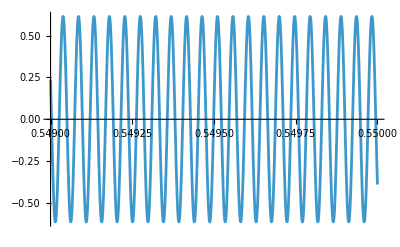

```mathematica
Plot[eIpsi2[x],{x,0.549,0.55}]
```